```mathematica
(* Radiative Quenching, Chapter 3 *)
(* This one uses my paper *)

(*electron mass *)
Subscript[m, e]=1;
(* Proton Mass *)
Subscript[m, p]=1836;
(* Reduced Mass *)
μ=Subscript[m, p]/2;
hbar= 1;  
hbarSI =1.054571817*^-34;
cLight=137.036 ;(*SpeedOfLight, atomic units*)
cLightSI= 299792458 ;(*SpeedOfLight, m/s*)
oneSec = 2.418884326509*^-17;  (* 1 sec SI <-> 1 sec AU *)
aBorh = 5.29177*^-11;   (* Si <-> AU *)

(* RawData format R,E, E + 1/R,A,p *)

vSg1RawData = Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1sV3.mx"];
vSu2RawData = Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/ungerade1sV3.mx"];



vSg1Data =vSg1RawData[[1;;44]];
vSu2Data = vSu2RawData[[1;;44]];

vSg1Data // MatrixForm
```

(0.2 | -6.50328 | -1.50328 | 7.42771 | 0.360646
0.3 | -5.81972 | -2.48639 | 19.2419 | 0.511749
0.4 | -5.27548 | -2.77548 | 19.3174 | 0.649645
0.5 | -4.8382 | -2.8382 | 19.3926 | 0.777673
0.6 | -4.48148 | -2.81481 | 19.4673 | 0.898146
0.7 | -4.18616 | -2.75759 | 19.5417 | 1.01272
0.8 | -3.93852 | -2.68852 | 19.6156 | 1.12264
0.9 | -3.72861 | -2.61749 | 19.6892 | 1.22886
1. | -3.54904 | -2.54904 | 1811.12 | 1.33211
1.1 | -3.39429 | -2.4852 | 1882.64 | 1.43302
1.5 | -2.95083 | -2.28416 | 20.1228 | 1.822
2. | -2.63638 | -2.13638 | 498.465 | 2.29625
2.5 | -2.4621 | -2.0621 | 20.8178 | 2.77382
3. | -2.36086 | -2.02753 | 580.234 | 3.25943
3.5 | -2.29798 | -2.01226 | 616.317 | 3.75168
4. | -2.25568 | -2.00568 | 21.8027 | 4.24799
4.5 | -2.22506 | -2.00284 | 682.247 | 4.74644
5. | -2.20156 | -2.00156 | 712.841 | 5.24591
6 | -2.16732 | -2.00065 | 154397. | 6.24594
7 | -2.14322 | -2.00036 | 20180. | 7.2463
8 | -2.12523 | -2.00023 | 5050.83 | 8.24666
9 | -2.11127 | -2.00016 | 20245.7 | 9.24697
10 | -2.10012 | -2.00012 | 5545.88 | 10.2472
11 | -2.09099 | -2.00009 | 20311.2 | 11.2475
12 | -2.08339 | -2.00006 | 156292. | 12.2476
13 | -2.07696 | -2.00004 | 20376.7 | 13.2478
14 | -2.07144 | -2.00001 | 507684. | 14.2478
15 | -2.06663 | -1.99996 | 157235. | 15.2478
16 | -2.06239 | -1.99989 | 7353.53 | 16.2476
17 | -2.0586 | -1.99978 | 157862. | 17.2473
18 | -2.05516 | -1.9996 | 508941. | 18.2465
19 | -2.05197 | -1.99934 | 509255. | 19.2453
20 | -2.04897 | -1.99897 | 158800. | 20.2434
21 | -2.04609 | -1.99847 | 20637.4 | 21.2406
22 | -2.04326 | -1.99781 | 510197. | 22.2367
23 | -2.04042 | -1.99695 | 510510. | 23.2313
24 | -2.03753 | -1.99587 | 160048. | 24.2242
25 | -2.03454 | -1.99454 | 160359. | 25.215
26 | -2.0314 | -1.99294 | 160669. | 26.2033
27 | -2.02809 | -1.99105 | 511764. | 27.1889
28 | -2.02456 | -1.98885 | 512077. | 28.1714
29 | -2.0208 | -1.98632 | 512390. | 29.1504
30 | -2.01679 | -1.98346 | 161909. | 30.1257
31 | -2.01251 | -1.98025 | 513016. | 31.0968)

0.00074606

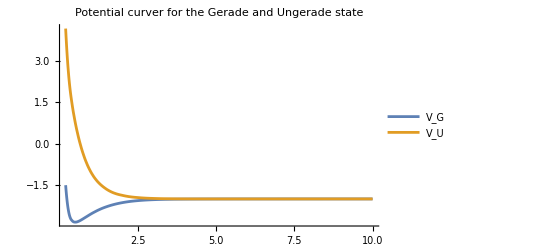

```mathematica
(* Load Potential curves for 1sg, 2sg states 
"R,E, E + 1/R,A,p *)
(* 1sg state, potential curve *)
vG=Interpolation[Transpose[{vSg1Data[[All,1]],vSg1Data[[All,3]]}], InterpolationOrder->3];
(* 2sg state, potential curve *)
vU=Interpolation[Transpose[{vSu2Data[[All,1]],vSu2Data[[All,3]]}], InterpolationOrder->3];

deltaV[r_]:=Abs[vG[r]-vU[r]];
deltaV[20]
Plot[{vG[r],vU[r]},{r,0.2,10}, PlotRange->Full, PlotLegends->{"V_G","V_U"}, PlotLabel->"Potential curver for the Gerade and Ungerade state"]
```

{1.,-3.54904,-2.54904,1811.12,1.33211}

Unset::wrsym: Symbol ⅇ is Protected.

NDEigensystem[{(-A-2 η+0.5 η^2) H[η]-2 η H'[η]+(1-η^2) H''[η],{H[-1]==0,H[1]==0,H'[0]==0}},H[η],{η,-1,1},3]

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at ξ == 1..

ReplaceAll::reps: {NDSolve[{2 ξ X'[ξ]+X[ξ] (Times[«2»]+Times[«2»]+Times[«2»]+Times[«3»]+Times[«2»])+(-1+Power[«2»]) X''[ξ]==0,X'[1]==0,X[10]==0},X,{ξ,1,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 1.00018 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{2.00037 X'[1.00018]+X[1.00018] (2.50055+Times[«2»]+Times[«3»]+Times[«2»])+0.000367748 X''[1.00018]==0,X'[1]==0,X[10]==0},X,{1.00018,1,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 1.00018 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{2.00037 X'[1.00018]+X[1.00018] (2.50055+Times[«2»]+Times[«3»]+Times[«2»])+0.000367748 X''[1.00018]==0.,X'[1.]==0.,X[10.]==0.},X,{1.00018,1.,10.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 1.18386 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

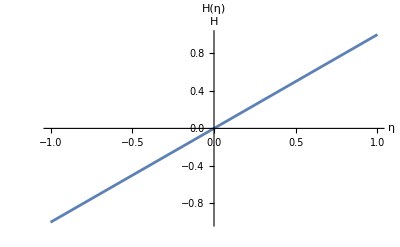

```mathematica
(* Get all Rs, and coefficients A and p and calculate D(R) for all Rs *)
(* RawData format R,E, E + 1/R,A,p *)
inputData = Transpose[{vSg1Data[[1;;maxIndex,1]],vSg1Data[[1;;maxIndex,4]],vSg1Data[[1;;maxIndex,5]],vSu2Data[[1;;maxIndex,4]],vSu2Data[[1;;maxIndex,5]]}];

maxIndex = 9;
vSg1Data[[maxIndex]]

R = 1;
ξmax=10;


(*Define symbolic separation constant and energy*)
A=.;E=.;


(*Equations from separation of variables*)
eqXi=D[(ξ^2-1) D[X[ξ],ξ],ξ]+(-E R^2 ξ^2+2 R ξ+A) X[ξ];
eqEta=D[(1-η^2) D[H[η],η],η]+(-E R^2 η^2-2 R η-A) H[η];


(*Boundary conditions*)
bcXi={X'[1]==0,X[ξmax]==0};
bcEta={H[-1]==0,H[1]==0,H'[0]==0 (*even parity/gerade*)};


(*Solve angular equation first (eigenvalue problem for A)*)
solEta=NDEigensystem[{eqEta/. {R->1,E->-0.5},(*trial energy*)bcEta},H[η],{η,-1,1},3]


(*Extract lowest eigenvalue for A and plug into xi equation*)
A0=solEta[[1,1]];
eqXiEval=eqXi/. {R->1,E->-0.5,A->A0};


(*Solve radial equation*)
solXi=NDSolve[{eqXiEval==0,Sequence@@bcXi},X,{ξ,1,ξmax}];


(*Normalize and plot*)
Plot[Evaluate[X[ξ]/. solXi],{ξ,1,ξmax},PlotLabel->"X(ξ)",AxesLabel->{"ξ","X"}]


Plot[Evaluate[solEta[[2,1]]],{η,-1,1},PlotLabel->"H(η)",AxesLabel->{"η","H"}]
```